```mathematica
1/(2π)Integrate[Exp[I kx x-I kx^2/(2 k)z],{kx,-∞,∞},Assumptions->Im[z/k]<0]*1/(2π)Integrate[Exp[I ky y-I ky^2/(2 k)z],{ky,-∞,∞},Assumptions->Im[z/k]<0]
```

-(ⅈ ⅇ^((ⅈ k x^2)/(2 z)+(ⅈ k y^2)/(2 z)) k)/(2 π z)

```mathematica
Integrate[r Exp[-I kx r Cos[ϕ]-I ky r Sin[ϕ]],{ϕ,0,2π}]
```

2 π BesselJ[0,√(kx^2+ky^2) r]

```mathematica
Integrate[2 π r BesselJ[0,k r],{r,0,a}]
```

(2 a π BesselJ[1,a k])/k

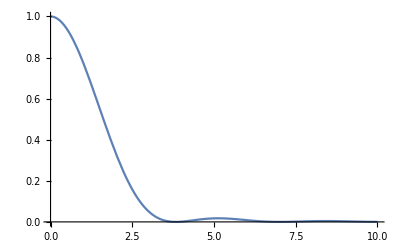

```mathematica
Plot[4(BesselJ[1,α]/α)^2,{α,0,10}]
```